```mathematica
SetDirectory[NotebookDirectory[]];
options3={Frame->{True,True,False,False},FrameStyle->Black,BaseStyle->{FontSize->30},LabelStyle->Black};
```

```mathematica
fNumericMean[aX_,α_,β_,y0_]:=Module[{y,x,f=NDSolveValue[{y'[x]==α y[x](1-β y[x]),y[0]==y0},y,{x,0,100}]},f[aX]]
fMean[x_,α_,β_,y0_]:=(ⅇ^(x α) y0)/(1-y0 β+ⅇ^(x α) y0 β)
fYGenerate[x_,α_,β_,y0_,σ_]:=RandomVariate[NormalDistribution[fMean[x,α,β,y0],σ],{1}][[1]]
```

```mathematica
lX =Table[x,{x,0,10,0.5}];
lY=fYGenerate[#,0.5,0.001,5,2]&/@lX;
```

## Get fake data

```mathematica
Needs["PolygonPlotMarkers`"]

allShapes=PolygonMarker[All]
Tooltip[Graphics[{FaceForm[Hue@Random[]],EdgeForm[{Black,Thickness[0.003],JoinForm["Miter"]}],PolygonMarker[#,1]},ImageSize->30,PlotRange->1.5,PlotRangePadding->0,ImagePadding->0],#]&/@allShapes
```

{TripleCross,Y,UpTriangle,UpTriangleTruncated,DownTriangle,DownTriangleTruncated,LeftTriangle,LeftTriangleTruncated,RightTriangle,RightTriangleTruncated,ThreePointedStar,Cross,DiagonalCross,Diamond,Square,FourPointedStar,DiagonalFourPointedStar,FivefoldCross,Pentagon,FivePointedStar,FivePointedStarThick,SixfoldCross,Hexagon,SixPointedStar,SixPointedStarSlim,SevenfoldCross,SevenPointedStar,SevenPointedStarNeat,SevenPointedStarSlim,EightfoldCross,Disk,H,I,N,Z,S,Sw,Sl}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
lX =Table[x,{x,0,10,0.5}];
lY=fYGenerate[#,0.5,0.05,5,2]&/@lX;
lY1=fYGenerate[#,0.5,0.05,5,2]&/@lX;
lY2=fYGenerate[#,0.5,0.05,5,2]&/@lX;
```

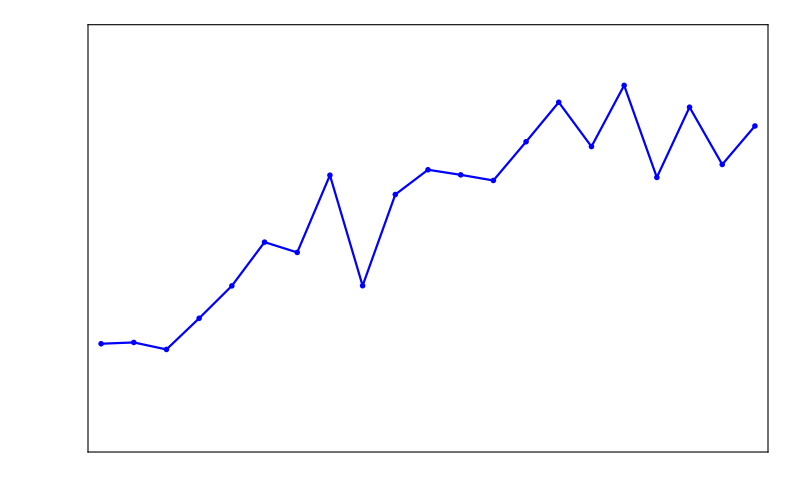

```mathematica
g1=ListLinePlot[{Thread[{lX,lY}]},PlotStyle->{Blue,Orange,Darker@Green},FrameStyle->Directive[Black,16,Thick],PlotRange->{Automatic,{0,25}},Evaluate@options3,PlotMarkers ->{Graphics[{FaceForm[Blue],Disk[{0,0},Scaled[0.07/Sqrt[π]]]},AlignmentPoint->{0,0}],Graphics[{FaceForm[Orange],Disk[{0,0},Scaled[0.05/Sqrt[π]]]},AlignmentPoint->{0,0}],
Graphics[{FaceForm[Darker@Green],Disk[{0,0},Scaled[0.05/Sqrt[π]]]},AlignmentPoint->{0,0}]},FrameLabel->None,ImageSize->800,FrameTicks->None]
```

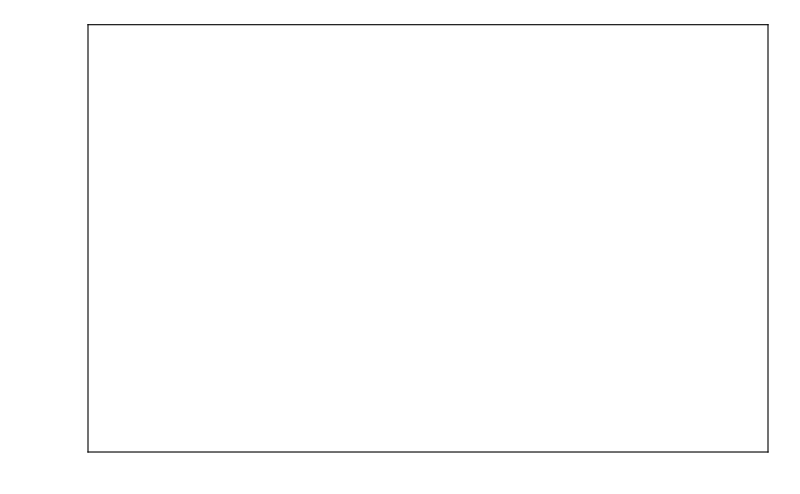

```mathematica
g1a=ListPlot[Thread[{lX,lY}],PlotStyle->{{Thickness[0.01],White},{Thickness[0.01],Orange},{Thickness[0.01],Magenta}},PlotRange->{Automatic,{0,25}},Evaluate@options3,PlotMarkers ->{Automatic,15},FrameLabel->None,ImageSize->800,FrameTicks->None]
```

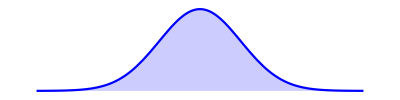

```mathematica
aPlot=Plot[PDF[NormalDistribution[0,1],x],{x,-4,4},Axes->None,PlotStyle->Blue,Filling->Bottom,AspectRatio->1/4]
```

```mathematica
aPlot1=Plot[PDF[NormalDistribution[0,4],x],{x,-10,10},Axes->None,PlotStyle->Blue,Filling->Bottom,AspectRatio->1/4];
aPlot2=Plot[PDF[NormalDistribution[0,0.5],x],{x,-4,4},Axes->None,PlotStyle->Blue,Filling->Bottom,AspectRatio->1/4];
aPlot3=Plot[PDF[NormalDistribution[0,3],x],{x,-8,8},Axes->None,PlotStyle->Blue,Filling->Bottom,AspectRatio->1/4];
aPlot4=Plot[PDF[NormalDistribution[0,5],x],{x,-13,13},Axes->None,PlotStyle->Blue,Filling->Bottom,AspectRatio->1/4];
```

```mathematica
g2=Show[g1a,Graphics[Inset[Rotate[aPlot,3Pi /2],{1,fMean[1.2,0.5,0.05,5]}]],
Graphics[Inset[Rotate[aPlot1,3 Pi/2],{1+2.67,fMean[1+2.5,0.5,0.05,5]}]],Graphics[Inset[Rotate[aPlot3,3 Pi/2],{1+2.7 2,fMean[5.5,0.5,0.05,5]}]],Graphics[Inset[Rotate[aPlot4,3 Pi/2],{9.5,18.4}]],FrameStyle->Directive[Black,16,Thick]]
```

-Graphics-

```mathematica
Export["../figures/logistic_full.pdf",g1]
```

../figures/logistic_full.pdf

```mathematica
Export["../figures/logistic_summary.pdf",g2]
```

../figures/logistic_summary.pdf

## Plot deterministic solution

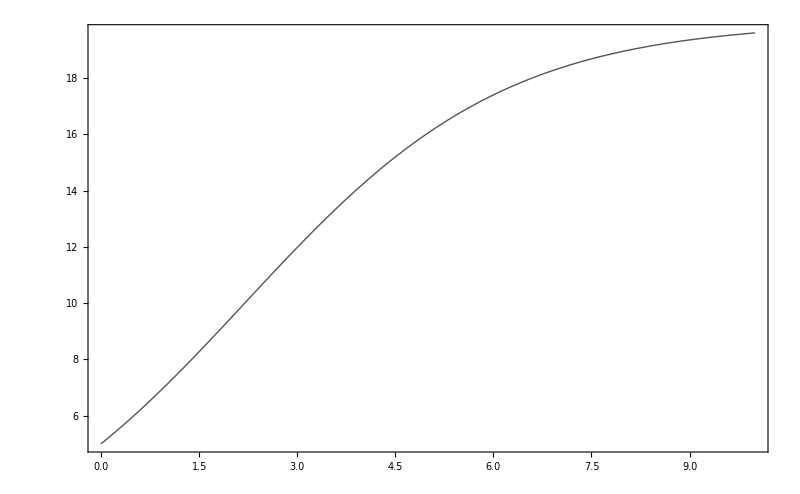

```mathematica
g1=Plot[fMean[x,0.5,0.05,5],{x,0,10},FrameLabel->None,ImageSize->800,FrameTicks->None,FrameStyle->Directive[Black,16,Thick],Frame->{True,True,False,False},PlotStyle->Directive[Thick,Darker@Gray]]
```

```mathematica
true=Table[fMean[x,0.5,0.05,5],{x,0,10,0.01}];
trueNoise=true+RandomVariate[NormalDistribution[0,1],Length@true];
```

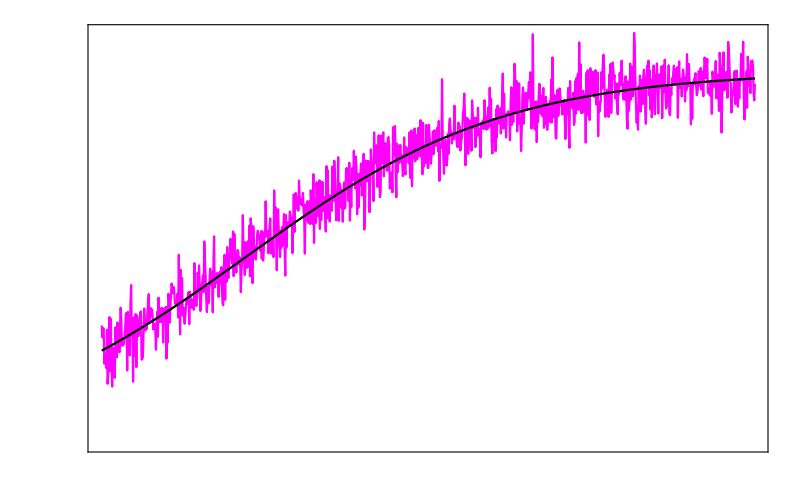

```mathematica
ListLinePlot[{trueNoise,true},Axes->None,PlotStyle->{Magenta,Black},FrameLabel->None,ImageSize->800,FrameTicks->None,FrameStyle->Directive[Black,16,Thick],Frame->{True,True,False,False},PlotStyle->Directive[Thick,Darker@Gray]]
```

```mathematica
Clear[fPDF]
```

```mathematica
fPDF[y_,x_,α_,β_,y0_,fSigma_]:=PDF[NormalDistribution[fMean[x,α,β,y0],fSigma[x]],y]
```

```mathematica
fSigma[x_]:=1
```

```mathematica
(ColorData[{"BeachColors","Reverse"}][#]&)
```

```mathematica
ContourStyle
```

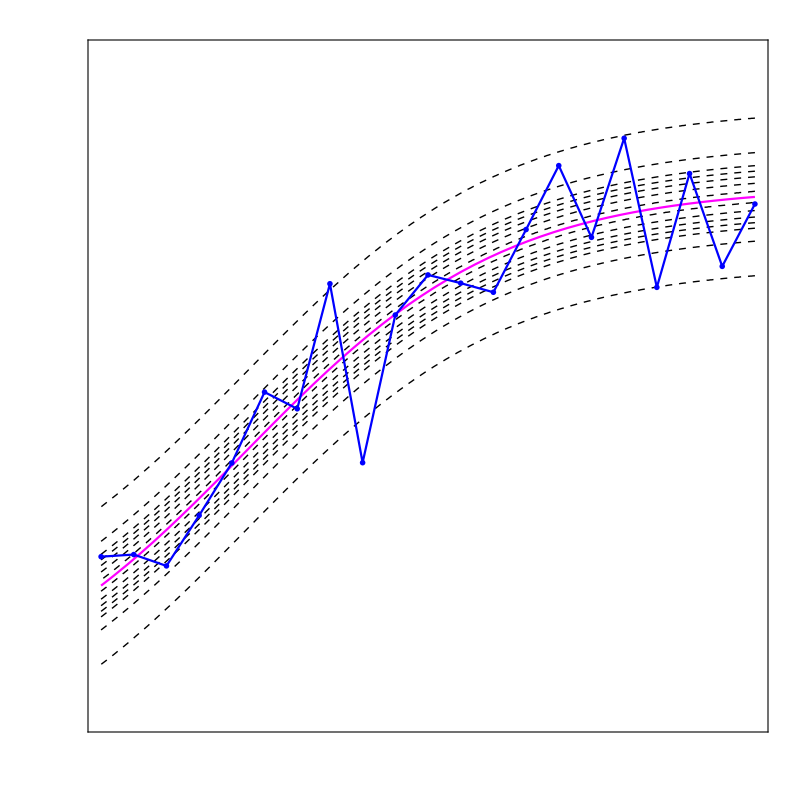

```mathematica
gFinal1=Show[ContourPlot[fPDF[y,x,0.5,0.05,5,fSigma],{x,0,10},{y,0,25},PlotPoints->100,PlotRange->Full,ContourShading->None,Contours->{0.005,0.1,0.2,0.25,0.3,0.35,0.39},ContourStyle->Dashed,Axes->None,FrameLabel->None,ImageSize->800,FrameTicks->None,FrameStyle->Directive[Black,16,Thick],Frame->{True,True,False,False}],Plot[fMean[x,0.5,0.05,5],{x,0,10},PlotStyle->Magenta],g1]
```

## Doing MCMC using noisy data

```mathematica
lX =Table[x,{x,0,10,0.5}];
lY=fYGenerate[#,0.5,0.05,5,3]&/@lX;
```

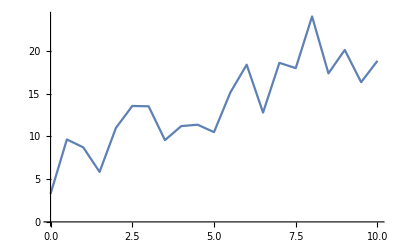

```mathematica
ListLinePlot[Thread[{lX,lY}]]
```

```mathematica
If[#<0,1,0]&/@({-1,2,3,4})
```

{1,0,0,0}

```mathematica
fLogLikelihood[lX_,lY_,α_,β_,y0_,σ_]:=Block[{lpred=fMean[#,α,β,y0]&/@lX,resid},resid=lY-lpred;LogLikelihood[NormalDistribution[0,σ],resid]]
fPrior[α_,β_,y0_,σ_]:=If[Total[If[#<0,1,0]&/@{α,β,y0,σ}]>0,0,1]
```

```mathematica
fStep[α_,β_,y0_,σ_,sigmaa_,sigmab_,sigmay0_,sigmasigma_]:=RandomVariate[MultinormalDistribution[{α,β,y0,σ},DiagonalMatrix[{sigmaa,sigmab,sigmay0,sigmasigma}]],1][[1]]
fStepAndAccept[lX_,lY_,α_,β_,y0_,σ_,sigmaa_,sigmab_,sigmay0_,sigmasigma_]:=Block[{lparams=fStep[α,β,y0,σ,sigmaa,sigmab,sigmay0,sigmasigma],u=RandomReal[],a1,b1,y1,σ1},a1=lparams[[1]];b1=lparams[[2]];y1=lparams[[3]];
σ1=lparams[[4]];
If[Exp[fLogLikelihood[lX,lY,a1,b1,y1,σ1] -fLogLikelihood[lX,lY,α,β,y0,σ] ] fPrior[a1,b1,y1,σ1] / fPrior[α,β,y0,σ]>u,{a1,b1,y1,σ1},{α,β,y0,σ}]]
fMCMC[numsteps_Integer,lX_,lY_,α_,β_,y0_,σ_,sigmaa_,sigmab_,sigmay0_,sigmasigma_]:=NestList[fStepAndAccept[lX,lY,#[[1]],#[[2]],#[[3]],#[[4]],sigmaa,sigmab,sigmay0,sigmasigma]&,{α,β,y0,σ},numsteps]
```

```mathematica
res=fMCMC[10000,lX,lY,0.5,0.05,5,3,0.1,0.005,0.5,0.3];
```

```mathematica
res1=DeleteDuplicates[res];
```

```mathematica
Length@res1
```

229

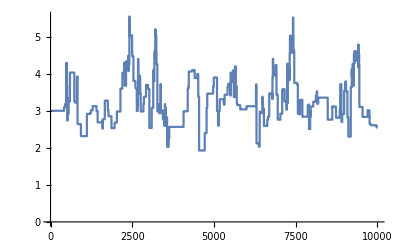

```mathematica
ListLinePlot[res[[All,4]]]
```

```mathematica
g1=Plot[fMean[x,#[[1]],#[[2]],#[[3]]],{x,0,10},PlotStyle->Opacity[1,ColorData["BrightBands"][RandomReal[]]],FrameLabel->None,ImageSize->800,FrameTicks->None,FrameStyle->Directive[Black,16,Thick],Frame->{True,True,False,False}]&/@res1[[1;;20]];
```

```mathematica
gFinal=Show[Show[g1a,Graphics[Inset[Rotate[aPlot,3Pi /2],{1,fMean[1.2,0.5,0.05,5]}]],
Graphics[Inset[Rotate[aPlot1,3 Pi/2],{1+2.67,fMean[1+2.5,0.5,0.05,5]}]],Graphics[Inset[Rotate[aPlot3,3 Pi/2],{1+2.7 2,fMean[5.5,0.5,0.05,5]}]],Graphics[Inset[Rotate[aPlot4,3 Pi/2],{9.5,18.4}]],FrameStyle->Directive[Black,16,Thick]],g1]
```

-Graphics-

```mathematica
Export["../figures/bayesian.pdf",gFinal1]
```

../figures/bayesian.pdf

```mathematica
Export["../figures/ourproblem.pdf",gFinal]
```

../figures/ourproblem.pdf

## Posteriors

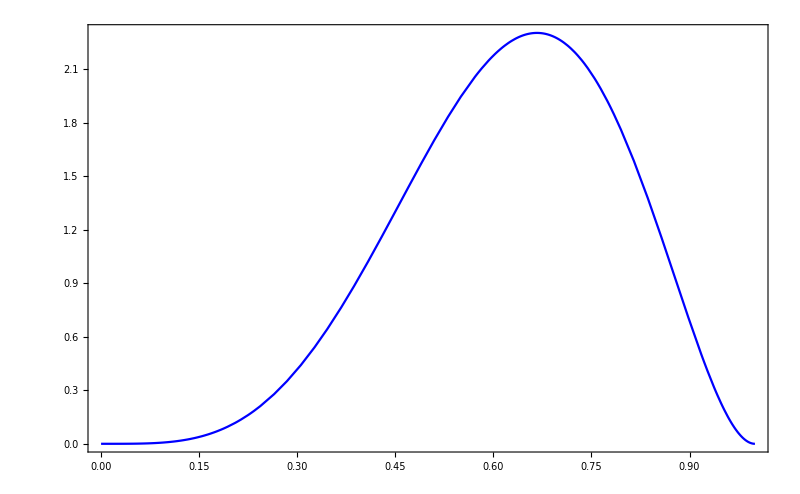

```mathematica
ga=Plot[PDF[BetaDistribution[5,3],θ],{θ,0,1},FrameLabel->None,ImageSize->800,FrameTicks->None,FrameStyle->Directive[Black,16,Thick],Frame->{True,True,False,False},PlotStyle->Blue]
```

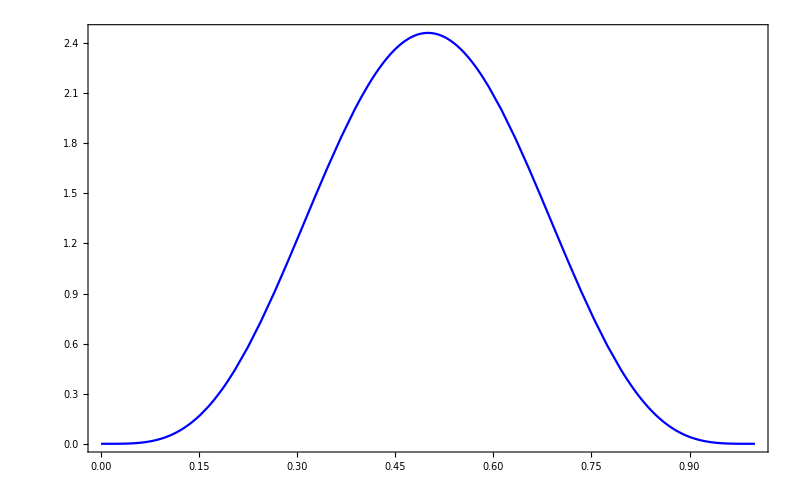

```mathematica
gb=Plot[PDF[BetaDistribution[5,5],θ],{θ,0,1},FrameLabel->None,ImageSize->800,FrameTicks->None,FrameStyle->Directive[Black,16,Thick],Frame->{True,True,False,False},PlotStyle->Blue]
```

```mathematica
Export["../figures/posterior1.pdf",ga]
Export["../figures/posterior2.pdf",gb]
```

../figures/posterior1.pdf

../figures/posterior2.pdf

## Hierarchical model figure

```mathematica
lX =Table[x,{x,{1,1+2.7,1+2 2.7, 9.5}}];
lY=fYGenerate[#,0.5,0.05,5,3]&/@lX;
```

```mathematica
fGenerateY[]:=Block[{lX =Table[x,{x,{1,1+2.7,1+2 2.7, 9.5}}],lY},lX=lX+RandomVariate[NormalDistribution[0,0.1],Length@lX];Thread[{lX,fYGenerate[#,0.5,0.05,5,3]&/@lX}]]
```

```mathematica
data=Table[fGenerateY[],{i,1,10,1}];
```

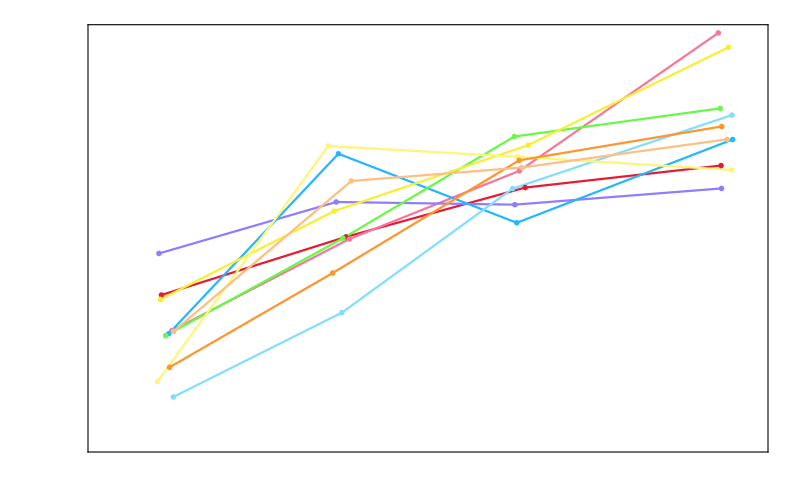

```mathematica
ga1=ListLinePlot[data,PlotStyle->"BrightBands",PlotRange->{{0,10},Full},Joined->True,PlotMarkers ->Graphics[{FaceForm[Blue],Disk[{0,0},Scaled[0.03/Sqrt[π]]]},AlignmentPoint->{0,0}],FrameLabel->None,ImageSize->800,FrameTicks->None,FrameStyle->Directive[Black,16,Thick],Frame->{True,True,False,False}]
```

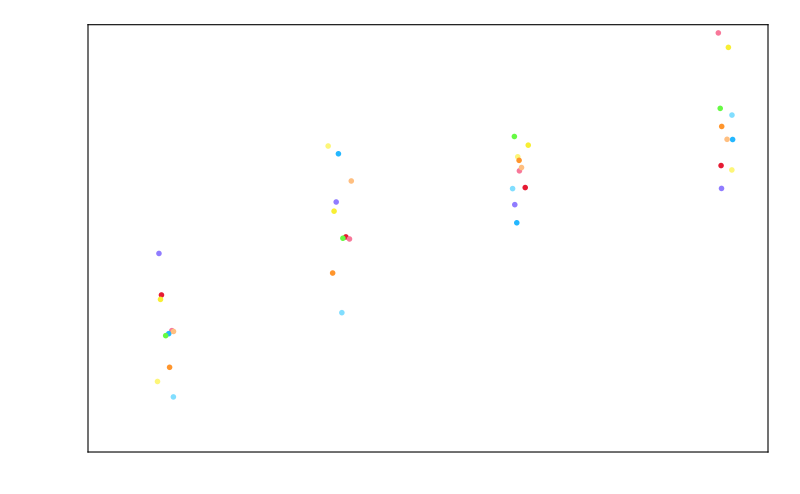

```mathematica
ga2=ListPlot[data,PlotStyle->"BrightBands",PlotRange->{{0,10},Full},PlotMarkers ->Graphics[{FaceForm[Blue],Disk[{0,0},Scaled[0.03/Sqrt[π]]]},AlignmentPoint->{0,0}],FrameLabel->None,ImageSize->800,FrameTicks->None,FrameStyle->Directive[Black,16,Thick],Frame->{True,True,False,False}]
```

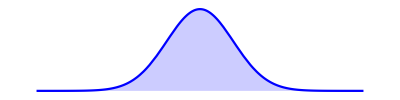
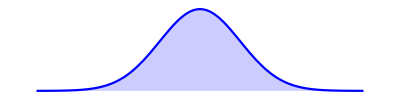
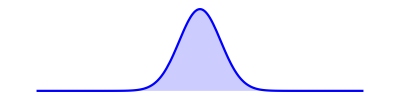
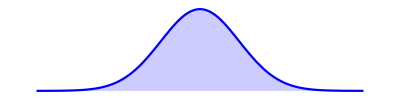
{{6.69044,-Graphics-},{13.4901,-Graphics-},{16.2131,-Graphics-},{19.2657,-Graphics-}}

```mathematica
lPlots={#[[1]],Plot[PDF[NormalDistribution[0,#[[2]]],x],{x,-12,12},Axes->None,PlotStyle->Blue,Filling->Bottom,AspectRatio->1/4]}&/@(FindDistributionParameters[#,NormalDistribution[μ,σ]][[All,2]]&/@Transpose@data[[All,All,2]])
```

```mathematica
g2=Show[g1a,Graphics[Inset[Rotate[aPlot,3Pi /2],{1,fMean[1.2,0.5,0.05,5]}]],
Graphics[Inset[Rotate[aPlot1,3 Pi/2],{1+2.67,fMean[1+2.5,0.5,0.05,5]}]],Graphics[Inset[Rotate[aPlot3,3 Pi/2],{1+2.7 2,fMean[5.5,0.5,0.05,5]}]],Graphics[Inset[Rotate[aPlot4,3 Pi/2],{9.5,18.4}]],FrameStyle->Directive[Black,16,Thick]]
```

```mathematica
ga3=Show[g1a,Table[Graphics[Inset[Rotate[lPlots[[i,2]],3Pi /2],{lX[[i]],lPlots[[i,1]]}]],{i,1,4,1}]]
```

-Graphics-